# MyPublisher/SamplePaclet

A complete sample Paclet

## Paclet

### Paclet Directory

NotebookDirectory[]

### Manifest

"Documentation"

"English"

"Guides"

"SampleGuide.nb"Documentation/English/Guides/SampleGuide.nb

"ReferencePages"

"Symbols"

"AddOne.nb"Documentation/English/ReferencePages/Symbols/AddOne.nb

"AddTwo.nb"Documentation/English/ReferencePages/Symbols/AddTwo.nb

"Tutorials"

"Arithmetic.nb"Documentation/English/Tutorials/Arithmetic.nb

"Kernel"

"AddOne.wl"Kernel/AddOne.wl

"AddTwo.wl"Kernel/AddTwo.wl

"SamplePaclet.wl"Kernel/SamplePaclet.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"README.md"README.md

"ResourceDefinition.nb"ResourceDefinition.nb

"Tests"

"AddOne.wlt"Tests/AddOne.wlt

"AddTwo.wlt"Tests/AddTwo.wlt

## Web Content

### Headline Image

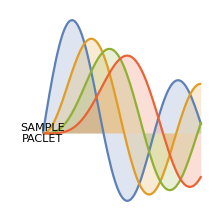

```mathematica
Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis,Epilog->Inset[Framed[Style[Column[{Style["SAMPLE",Italic],Style["PACLET",Bold]},Alignment->Center,Spacings->.15],FontSize->30],Background->White]],AspectRatio->1,Axes->False]
```

### Basic Description

This is a sample paclet used for PacletCICD documentation examples. This paclet is meant to demonstrate basic CI/CD workflows for typical paclet layouts.

### Details

This paclet contains two uninteresting functions.

There is not much else to say about it.

### Main Guide Page

"Documentation/English/Guides/SampleGuide.nb"

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[];
```

```mathematica
Needs[];
```

### Basic Examples

Here is a basic example:

```mathematica
AddOne[1]
```

2

Here's another example for a different function:

```mathematica
AddTwo[1]
```

3

Create a very interesting Plot:

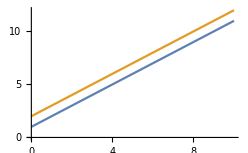

```mathematica
Plot[{AddOne[x],AddTwo[x]},{x,0,10}]
```

### Scope

Add to symbols:

```mathematica
AddOne[x]
```

1+x

```mathematica
AddTwo[x]
```

2+x

Create new functions that no one has ever thought of before:

```mathematica
addThree=AddOne@*AddTwo
```

AddOne@*AddTwo

```mathematica
addThree[1]
```

4

```mathematica
naturalNumber[n_]:=Nest[AddOne,0,n];
```

Simply incredible:

```mathematica
naturalNumber[5]
```

5

### Applications

Reinvent arithmetic:

```mathematica
plus[x_,y_]:=Nest[AddOne,x,y];
```

```mathematica
plus[3,4]
```

7

```mathematica
times[x_,y_]:=Nest[OperatorApplied[plus][x],0,y];
```

```mathematica
times[3,4]
```

12

Weird numbers like negative integers and reals are too hard and can therefore be assumed to not exist.

### Properties and Relations

AddTwo can be implemented using only AddOne:

```mathematica
AddTwo[x]
```

2+x

```mathematica
addTwo=AddOne@*AddOne;
```

```mathematica
addTwo[x]
```

2+x

AddOne is the best function:

```mathematica
[Row[{AddOne," is simply the best"}]]
```

-Graphics-

## Source & Additional Information

### Creator

Example Author

### Source Control Repository

https://github.com/rhennigan/PacletCICD-Examples-Sample

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

sample

paclet

CI/CD

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

Wolfram/PacletCICD

### Source/Reference Citation

Source, reference or citation information

### Links

GitHub - rhennigan/PacletCICD: Continuous integration and deployment for Wolfram Language Paclets

GitHub - rhennigan/PacletCICD-Examples-Sample

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

### Disclosures

DisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more informationLocal files

DisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more informationWolfram account

DisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more informationExternal services

DisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates, modifies or deletes symbols outside of the Publisher`PacletBaseName` context
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more informationWL system configuration

DisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more informationOS configuration

DisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more informationLocal system interactions

DisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more informationOther

## Author Notes

Additional information about limitations, issues, etc.